```mathematica
findConvexHullCoordsConvexPolysAS[polyObstacle_,polyRobot_]:=Module[{pts},
(* this function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Jan 2, 2019*)
(*First, place the robot at each vertix of the obstacle, and record the vertices coordinates, then flatten this list*)
pts =Flatten[ Table[polyObstacle⟦1,i⟧- polyRobot⟦1,j⟧,{i,1,Length[polyObstacle⟦1⟧]},{j,1,Length[polyRobot⟦1⟧]}],1];
(*second, grab an ordered list of convex hull of these points*)#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts]
]
```

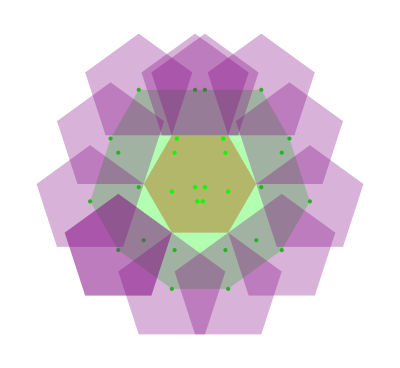

```mathematica
region1=Polygon[CirclePoints[6]];
robot=Polygon[CirclePoints[5]];
Graphics[{
Opacity[0.4],
Red,region1,
(*Blue,robot,*)
Opacity[1],Green,


(*find the coordinates of the convex hull:*)

pts =Flatten[Table[ Table[region1⟦1,i⟧-robot⟦1,j⟧,{i,1,Length[region1⟦1⟧]}],{j,1,Length[robot⟦1⟧]}],1];cvhullPt=#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts];
Point[pts],

Opacity[0.3],
Polygon[findConvexHullCoordsConvexPolysAS[region1,robot]],
(* draw the robot at the corners of the convex hull*)
Purple,
Table[Polygon[cvhullPt⟦i⟧+#&/@ robot⟦1⟧],{i,1,Length[cvhullPt]}]
}]
```